```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["sampledata.txt","TSV"];
```

```mathematica
extractData[{{"------------------------------------"},{__,numThreads_},{__,throughput_},{__,latency_},{__,successfulRatio_},{__,customerRatio_},{__,successfulCustomerRatio_},{"------------------------------------"},rs__}]:=
Prepend[extractData[{rs}],{numThreads,throughput,latency,successfulRatio,customerRatio,successfulCustomerRatio}];
extractData[{{_},rs__}]:=extractData[{rs}];
extractData[{}]:={};
```

```mathematica
extracted=extractData[data];
```

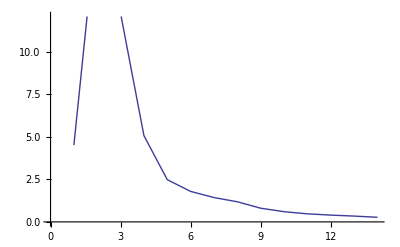

```mathematica
throughputGraph=ListLinePlot[{#[[1]],#[[2]]}&/@extracted]
```

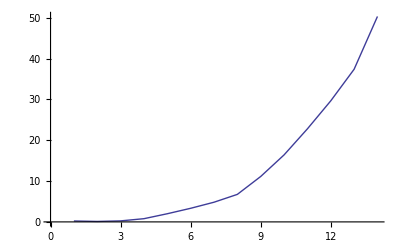

```mathematica
latencyGraph=ListLinePlot[{#[[1]],#[[3]]}&/@extracted]
```